```mathematica
(*参数设置*)pa=100000;(*外界压强，单位：Pa*)vc=0.01;(*容器容积，单位：m^3*)vp=0.001;(*活塞最大容积，单位：m^3*)r=vp/vc;(*比例系数*)n=50;(*打气次数*)(*容器压强函数*)pk[0]=pa;
pk[k_]:=pa*(1+k*r);
(*每次打气的功*)
W[k_]:=Module[{pPrev,pCurr},pPrev=pk[k-1];
pCurr=pk[k];
pa*vp*Log[pPrev/pa]+pCurr*vc*Log[pCurr/pPrev]];
(*计算总功*)
totalWork=Sum[W[k],{k,1,n}];
N[totalWork]
```

10750.6

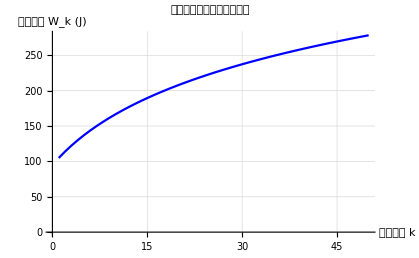
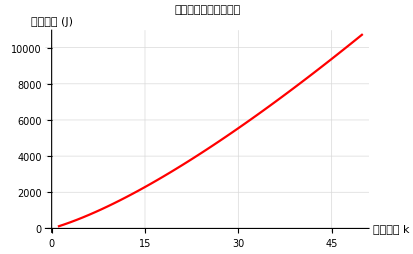

总功: 10750.6 J

```mathematica
(*计算每次做功和累计做功*)workData=Table[W[k],{k,1,n}];
cumulativeWork=Accumulate[workData];
(*绘制每次做功随次数的变化图*)
plot1=ListPlot[workData,PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"打气次数 k","每次做功 W_k (J)"},PlotLabel->"每次打气做功随次数的变化",GridLines->Automatic,Joined->True,PlotRange->All];
(*绘制累计做功随次数的变化图*)
plot2=ListPlot[cumulativeWork,PlotStyle->{Red,PointSize[Medium]},AxesLabel->{"打气次数 k","累计做功 (J)"},PlotLabel->"累计做功随次数的变化",GridLines->Automatic,Joined->True,PlotRange->All];
(*同时显示两个图表*)
Row[{plot1,plot2}]
(*计算总功*)
totalWork=cumulativeWork[[-1]];
Print["总功: ",N[totalWork]," J"]
```